# Лабораторная работа №8

## Грицак Александра, ПО-4

Прямая интеграция реляционных баз данных в свою работу может усложниться по ряду причин. Во-первых, многие эксперты не обладают знанием SQL, необходимыми для непосредственного использования реляционных баз данных. Во-вторых, существуют различия между диалектами SQL и поддерживаемыми наборами функций для различных серверных частей баз данных. По этим причинам тесная интеграция реляционных баз данных непосредственно в язык очень полезна. Это позволяет пользователям сосредоточиться на решении своих проблем, а не на предоставлении технической инфраструктуры.
В Wolfram, для огромного количества случаев, когда нужно запрашивать базу данных, можно взаимодействовать с базой данных через высокоуровневые запросы Entity Framework, построенные с использованием языка функциональных запросов Entity framework. Затем платформа отвечает за перевод запроса на соответствующий диалект SQL, выполнение его на стороне базы данных и возврат результатов обратно пользователю в соответствующем формате. Entity Framework для Wolfram в контексте реляционных баз данных во многом похож на то, что представляют собой объектно-реляционные отображения (ORM) для других языков. Несколько упрощая, сущности сопоставляются с отдельными строками таблиц базы данных, классы сущностей сопоставляются с таблицами базы данных, а свойства сущностей сопоставляются со столбцами базы данных. 

Чтобы начать работать с реляционной базой данных, нужно сначала создать ссылку для соединения с ней. Используем для этого DatabaseReference.

```mathematica
conn = DatabaseReference[URL["mysql://root@localhost:3306/students"]]
```

DatabaseReference[…]

С помощью функции DatabaseConnect или [“Connect”] попробуем установить соединение с базой данных по ранее созданной ссылке.

```mathematica
conn["Connect"]
```

Success[…]

Проверим, действительно ли прошло соединение с базой данных.

```mathematica
conn["Connected"]
```

True

```mathematica
rdb = RelationalDatabase[conn]
```

Создадим с помощью функции RelationalDatabase объект RelationalDatabase. Он содержит полную структуру базы данных, на которую мы ссылаемся (таблицы, колонки, ограничения и так далее) и он может быть использован как для визуального осмотра, так и для программного вытягивания этой информации, которая нам интересна.

RelationalDatabase[…]

Вытянем просмотренную выше информацию программным способом. Задав параметр “Tables” можно получить список все таблиц в базе данных.

```mathematica
rdb["Tables"]
```

{student,univercity}

Граф связи сущностей:

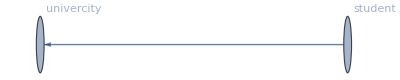

```mathematica
Graph[Join@@(Thread[#->rdb[#,"ForeignKeys","ToTable"]]&/@rdb["Tables"]),VertexLabels->"Name"]
```

Также можно проверить, существует ли указанная таблица в базе данных. Для этого нужно указать название предполагаемой таблицы и “Exists”.

```mathematica
rdb["student", "Exists"]
```

True

```mathematica
rdb["marks", "Exists"]
```

False

Задав как параметр название существующей таблицы и “Columns”, можно получить список всех столбцов данной таблицы.

```mathematica
rdb["student", "Columns"]
```

{id,first_name,last_name,city,date,univ_id}

Аналогично проверке на наличие таблицы, можно сделать проверку на наличие определенного столбца.

```mathematica
rdb["student", "first_name", "Exists"]
```

True

```mathematica
rdb["student", "address", "Exists"]
```

False

свойства колонки

```mathematica
rdb["student", "id", "Properties"]
```

{NativeTypeString,Default,Indexed,Name,Nullable}

Напоследок, можно получить список всех свойств определенной колонки таблицы, а также их значения.

```mathematica
rdb["student", "id",All]
```

<|NativeTypeString→INTEGER,Default→None,Indexed→False,Name→id,Nullable→False|>

Создадим поддерживаемой базой данных объект EntityStore из объекта RelationalDatabase. В нем будут находится все сущности, которые находятся в нужной нам базе данных.

```mathematica
es = EntityStore[rdb]
```

EntityStore[…]

Затем зарегистрируем сущности в объекте EntityStore, чтобы можно было получить к ним доступ напрямую через Entity.

```mathematica
EntityRegister[es]
```

{student,univercity}

Теперь можно начинать работу с самими таблицами в базе данных.
Для примера извлечем из таблицы student фамилию и дату рождения студента . Для этого используется функция EntityValue. Он используется для выполнения запроса и возвращает результат в различных формах. Первым параметром укажем сущность (таблицу) student, которая недавно была зарегистрирована, а вторым параметром - список извлекаемых свойств (полей) сущности.

```mathematica
EntityValue["student", {"first_name", "date"}]
```

{{Ivanov,Mon 20 Oct 2025},{Petrov,Thu 20 Jan 2022}}

Добавим параметр “PropertyAssociation”, чтобы к возвращаемым значениям еще добавлялись названия свойств.

```mathematica
EntityValue["student", {"first_name", "date"}, "PropertyAssociation"]
```

{<|first_name→Ivanov,date→Mon 20 Oct 2025|>,<|first_name→Petrov,date→Thu 20 Jan 2022|>}

Получим результат в виде таблицы значений.

```mathematica
EntityValue["student", {"first_name", "last_name", "date"}, "Dataset"]
```

В некоторых случаях может понадобиться получить список сущностей, содержащихся в типе или классе. Это можно сделать через EntityList.

```mathematica
EntityList["student"]
```

{1,2}

Кроме извлечения существующих свойств, можно также извлекать вычисляемые свойства - те свойства, которые вычисляются на лету. Такие свойства должны быть выражены через функцию EntityFunction. Выведем фамилию и имя  в одно поле через тире.

```mathematica
EntityValue["student", {
 EntityFunction[o, StringJoin[o["first_name"]," - ", o["last_name"]]]}]
```

{{Ivanov - Ivan},{Petrov - Petr}}

Если по какой-либо причине ранее зарегистрированные сущности нам будут не нужно, то их можно просто-напросто удалить. Для этого используется функция EntityUnregister.

```mathematica
EntityUnregister[es]
```

После завершения работы с базой данных, желательно разорвать соединение с ней. Функция DatabaseDisconnect используется для это, а в качестве параметра передается ссылка соединения с ней, созданная в самом начале.

```mathematica
conn["Disconnect"]
```

Success[…]